# Explorations: Generative Graphics

A lot of places have funky, repetitive designs. Some classic examples are bus seats and bowling alleys (seen below).

Drawing inspiration from these images, create your own! Start by trying to re-create the simple pattern below (or something similar).

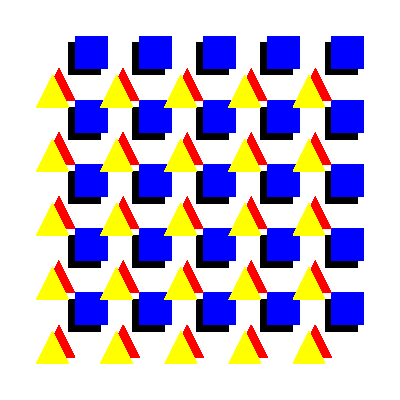

While you could create this image by individually placing graphics objects, figure out how you can create this kind of pattern by taking advantage of its repetitive structure.

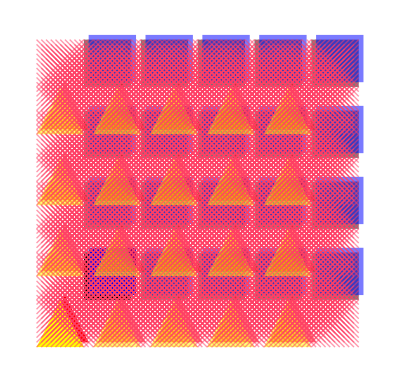

```mathematica
myPattern=Graphics[Flatten[{Table[{

Red, Triangle[{{x+0.1, y+0.1}, {x+0.6, y+1.1}, {x+1.1, y+0.1}}],
Yellow, Triangle[{{x, y}, {x+0.5, y+1}, {x+1, y}}],
Black, Rectangle[{x+1, y+1}, {x+2, y+2}],
Blue, Rectangle[{x+1.1, y+1.1}, {x+2.1, y+2.1}],

Table[{RGBColor[1,0.25,0.4,0.52],Line[{{x+i, y+j}, {x+1+i, y+1+j}}]}, {i, 0, 1, 0.1}, {j, 0, 1, 0.1}],
Table[{RGBColor[1,0.25,0.4,0.52],Line[{{x+i+1, y+j}, {x+i, y+1+j}}]}, {i, 0, 1, 0.1}, {j, 0, 1, 0.1}]
},
{x, 0, 5, 1.2}, {y, 0, 5, 1.5}]
}

]]
```

#### Design your own!

Why do these places have these chaotic designs? So they can be funky, in more than just aesthetics. Carpets and seats in these areas are in high traffic and potentially messy locations; these designs and colors help mask the visibility of stains.

Our basic design is okay at hiding a stain:

```mathematica
stain=-Graphics-;
```

But one of our real-life examples seem to do a better job, subjectively:

Now that you’ve got some experience creating a repeating pattern, try designing your own fabric! Keep in mind the goal of these designs and see if you can make one that is as good (or better!) at hiding the stain as the real-life example.

Want an extra challenge? Try to come up with a way to quantify or test how well the stain is hidden.

```mathematica
ImageCompose[myPattern, stain]
```

-Graphics-